При n = 2

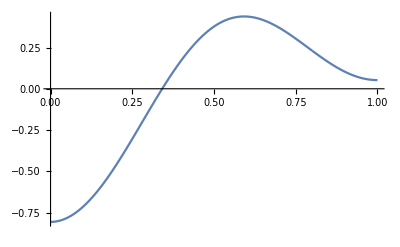

При n = 5

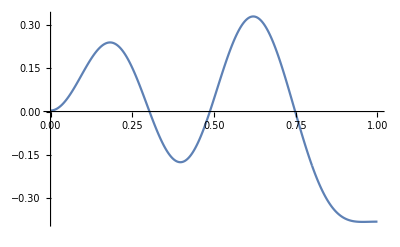

При n = 10

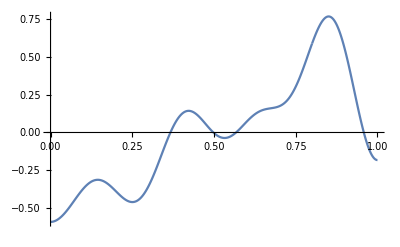

При n = 50

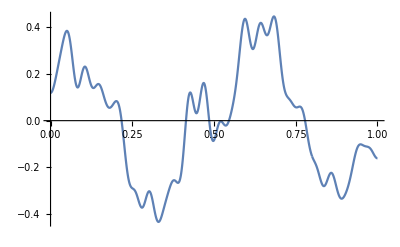

При n = 100

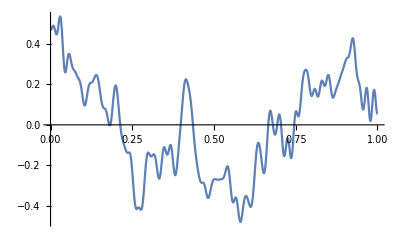

При n = 500

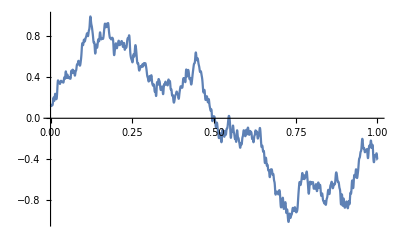

При n = 1000

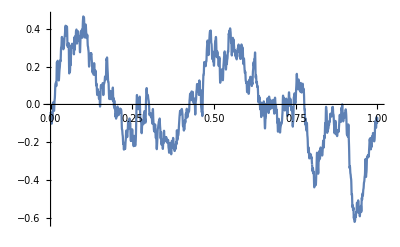

```mathematica
maxt=10000; (*Для разбиения отрезка [0,1] на равные интервалы*)
(*Вводим данные, согласно условию*)
(*Невозрастающая последовательность собственных чисел ковариационного оператора*)
λ[k_]:=1/(π^2 k^2);
(*Соотвтетствующие собственным числам собственные функции*)
(*Subscript[Κψ, k]=Subscript[λ, k] Subscript[ψ, k]  k=1,2,...*)
ψ[k_, t_]:=√2 Cos[π k t];
(*Массив значений для n*)
NUMS={2, 5, 10, 50, 100, 500, 1000};
(*Цикл по значеним заданным в NUMS*)
For[i = 1, i <= Length[NUMS], i++,
(*Значение для n-ранговой апроксимации берутся из NUMS*)
n=NUMS[[i]];
(*Генерируем последовательность n случайных величин распределенных по нормальному закону*)
ξ=RandomVariate[NormalDistribution[0,1],n];
(*Разложение Кархунена-Лоэва для заданного гауссовского процесса W^C(t)=W(t)-∫_0^1 W(s)ⅆs*)
W[t_]=∑_(k=1)^n √λ[k]*ψ[k, t]*ξ[[k]];
Print["При n = ",n];
(*Составляем таблицу значений функции с шагом t в 1/maxt*)
Print[ListLinePlot[Table[{s/maxt,W[s/maxt]},{s,0,maxt}]]];
]
```